{{u→InterpolatingFunction[{{0.,2.}},<>]}}

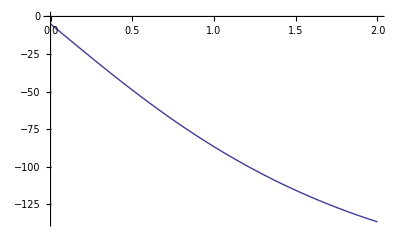

```mathematica
thresh = -10 ;
u0 = -5;
deltaT = 100;
eL = -200;

NDSolve[{u'[t]==(eL-u[t])+deltaT  Exp[(u[t]-thresh)/deltaT], u[0]==u0},u,{t,0,2}]
Plot[Evaluate[u[t]/.%],{t,0,2}]
```